#### BC_DirectPath.nb (formerly TrivPathToIso.nb) Find the shortest (direct) path between two elastic maps INSTRUCTIONS: Run common_funs.nb, ChooseTmat.nb, then this notebook Variables to change: Tmat, dt, ListSigma

#### choose Tmat

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatIgel;
```

```mathematica
Tmat=TmatSSA2023;
```

```mathematica
Tmat=TmatBrownAn00;
```

#### check that it’s symmetric, display info

```mathematica
MatrixNote[Tmat]
Tmat==Transpose[Tmat]
PrintVoigt[Tmat]
```

T is BrownAn00

True

The [T]_𝔹𝔹 matrix is (50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

The eigenvalues are: {204.263,179.169,75.8705,60.7101,50.1339,33.4538}

The Voigt matrix is (68.3 | 32.2 | 30.4 | 4.9 | -2.3 | -0.9
32.2 | 184.3 | 5. | -4.4 | -7.8 | -6.4
30.4 | 5. | 180. | -9.2 | 7.5 | -9.4
4.9 | -4.4 | -9.2 | 25. | -2.4 | -7.2
-2.3 | -7.8 | 7.5 | -2.4 | 26.9 | 0.6
-0.9 | -6.4 | -9.4 | -7.2 | 0.6 | 33.6)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.454 = 26.037^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

#### KEY FUNCTION

```mathematica
TT[t_,Tmat1_,Tmat2_]:=(1-t) Tmat1+t Tmat2
```

## Check between distances, angles, and norms

```mathematica
MatrixNote[Tmat]
Ranget
```

T is BrownAn00

{0.,0.2,0.4,0.6,0.8,1.}

#### changing the size of the elastic map changes distances but not angles

```mathematica
(*Tmat=2TmatBrownAn00;*)
```

#### choose a Sigma (choosing ISO will be instant; anything else may take time)

```mathematica
Sigx=ISO;
```

#### check on distances (linear with t)

```mathematica
dT[TT[#,Tmat,TISO],Sigx]&/@Ranget
(1-#)NormMatrix[Tmat-Closest[Tmat,Sigx]]&/@Ranget
```

{129.395,103.516,77.6371,51.7581,25.879,0.}

{129.395,103.516,77.6371,51.7581,25.879,0.}

#### beta angles

```mathematica
βT[TT[#,Tmat,TISO],Sigx]/Degree&/@Ranget
```

{26.0366,21.3465,16.3366,11.0568,5.58035,0}

#### norm of the elastic maps (independent of Sigx)

```mathematica
NormMatrix[TT[#,Tmat,TISO]]&/@Ranget
```

{294.787,284.38,276.014,269.88,266.132,264.87}

#### calculate the distances from the angles and norms

```mathematica
Sin[βT[TT[#,Tmat,TISO],Sigx]]NormMatrix[TT[#,Tmat,TISO]]&/@Ranget
```

{129.395,103.516,77.6371,51.7581,25.879,0.}

## Specify start/end elastic maps and Sigmas

#### Set of Sigmas to use For the plotting, it’d be helpful to list these in order from TRIV (smallest beta) to ISO (largest beta). These ListSigma will get over-written by the Special Cases below.

```mathematica
ListSigma={ORTH,TET};
```

```mathematica
ListSigma={ISO,CUBE,XISO,TRIG,TET,ORTH,MONO,TRIV};
```

```mathematica
ListSigma={MONO,ISO};
```

```mathematica
ListSigma={TRIV,MONO,TRIG,ORTH,TET,CUBE,XISO,ISO};  (* default *)
```

#### Closest T to ISO

```mathematica
MatrixNote[Tmat]
betaISO =βTinitial[Tmat,ISO]/Degree  (* AngleMatrix[Tmat,Closest[Tmat,ISO]]/Degree *)
TISO =Closest[Tmat,ISO];  (* ProjToVSigOfU[Tmat,id,ISO]*)
MatrixForm[TISO]
```

T is BrownAn00

26.0366

(82.8667 | 0 | 0 | 0 | 0 | 0
0 | 82.8667 | 0 | 0 | 0 | 0
0 | 0 | 82.8667 | 0 | 0 | 0
0 | 0 | 0 | 82.8667 | 0 | 0
0 | 0 | 0 | 0 | 82.8667 | 0
0 | 0 | 0 | 0 | 0 | 189.267)

#### Choose Tmat1 (low symmetry) and Tmat2 (high symmetry)

```mathematica
MatrixNote[Tmat]
Tmat1 =Tmat ;
Tmat2 =TISO;
```

T is BrownAn00

#### defaults for custom plotting (these will get overwritten below)

```mathematica
Sig1=TRIV;
Sig2=ISO;
ttop = 0.5;
```

#### choose t values (note: you can choose to use t1 < 0 for most of the maps in ChooseTmat.nb)

```mathematica
Print["minimum allowable t is t1 = ",tpertTmat[Tmat] ];
```

minimum allowable t is t1 = -0.66

```mathematica
(* Ranget=Join[{0},Range[t1,t2,dt],{1}] *)
```

```mathematica
t1 = 0.; t2 = 1.
dt=0.2; 
(*dt  0.05;*)
(* t1 = 0.8; t2 = 0.9;dt=0.01; *)
Ranget=Range[t1,t2,dt];
```

#### BrownAn00

```mathematica
(* t1 = -0.6;t2 = 1;dt=0.2; 
Ranget=Range[t1,t2,dt]; *)
```

#### Special Case 1: BrownAn00 TET triangle (supp1) TET to XISO segment for the Brown map Here TXISO is the closest to TRIV (nm2), and β_XISO = 20.35^o

```mathematica
(*MatrixNote[Tmat]
Sig1=TET;
Sig2=XISO;
MinimizationFacts[Tmat,Sig1]
TTET=Closest[Tmat,Sig1];
MinimizationFacts[Tmat,Sig2]
TXISO=Closest[Tmat,Sig2];
Tmat1=TTET;
Tmat2=TXISO; 
ListSigma={TET}; (* TET will give the triangle *)
ListSigma={MONO,TET,XISO}; 
ttop = 0.611707;*)
```

T is BrownAn00

#### Special Case 2: BrownAn00 TET parabola (supp2) TET to CUBE segment for the Brown map Here TCUBE is the closest to TRIV (nm2), and β_CUBE = 24.34^o

```mathematica
(*MatrixNote[Tmat]
Sig1=TET;
Sig2=CUBE; 
MinimizationFacts[Tmat,Sig1]
TTET=Closest[Tmat,Sig1];
MinimizationFacts[Tmat,Sig2]
TCUBE=Closest[Tmat,Sig2];
Tmat1=TTET ;
Tmat2=TCUBE;
ListSigma={MONO,TET};*)
```

#### Special Case 3: BrownAn00 TRIG triangle (supp3) TRIG to CUBE segment for the Brown map Here CUBE is the closest to TRIV (nm2), and β_CUBE = 21.12^o

```mathematica
(*MatrixNote[Tmat]
Sig1=TRIG;
Sig2=CUBE; 
MinimizationFacts[Tmat,Sig1]
TTRIG=Closest[Tmat,Sig1];
MinimizationFacts[Tmat,Sig2]
TCUBE=Closest[Tmat,Sig2];
Tmat1=TTRIG;
Tmat2=TCUBE;
ListSigma={MONO,TET,TRIG};
ttop=0.53515;*)
```

#### Special Case 4: BrownAn00 TET triangle (supp4) Experiment with different U to see if the triangle is sustained.

```mathematica
(*MatrixNote[Tmat]
MinimizationFacts[Tmat,XISO]
UXISO=UT[Tmat,XISO];
UforNM1=UXISO;
(* UforNM1=UXISO.ZRot[25Degree]; *)
(* UforNM1=UXISO.XRot[1Degree].YRot[1Degree].ZRot[1Degree]; *)
Sig1=ORTH;
Sig2=TET;
TORTH=ProjToVSigOfU[Tmat,UforNM1,Sig1];
TTET=ProjToVSigOfU[Tmat,UforNM1,Sig2];
Tmat1=TORTH;
Tmat2=TTET; 
ListSigma={TET};  (* no need to run MONO here, since betaMONO = 0 by design *)
ttop=0.310400;*)
```

#### Special Case 5: Igel XISO inverted triangle (supp5) version 1: t1=0, t2=1, dt=0.05 version 2: t1=0.8, t2=0.9, dt=0.01

```mathematica
(*MatrixNote[Tmat]
MinimizationFacts[Tmat,XISO]
UXISO=UT[Tmat,XISO];
UforNM1=UXISO;
Sig1=TET;
Sig2=CUBE;
TTET=ProjToVSigOfU[Tmat,UforNM1,Sig1];
TCUBE=ProjToVSigOfU[Tmat,UforNM1,Sig2];
Tmat1=TTET;
Tmat2=TCUBE; 
ListSigma={XISO};   (* no need to run MONO here, since betaMONO = 0 by design *)
ttop=0.8499757596500602;  (* solved in BC_XISObetweenTETandCUBE.nb *)*)
```

#### Special Case 6: SSA2023 TET and ORTH curves

```mathematica
(*MatrixNote[Tmat]
Sig1=MONO;
Sig2=TRIG;
MinimizationFacts[Tmat,Sig1]
TMONO=Closest[Tmat,Sig1];
MinimizationFacts[Tmat,Sig2]
TTRIG=Closest[Tmat,Sig2];
Tmat1=TMONO;
Tmat2=TTRIG; 
ListSigma={MONO,ORTH,TET};*)
```

#### check endpoints (but not that your chosen t values may exclude the endpoints)

```mathematica
MatrixNote[Tmat]
DispMat[Tmat1,2]
DispMat[TT[0,Tmat1,Tmat2],2]
DispMat[Tmat2,2]
DispMat[TT[1,Tmat1,Tmat2],2]
```

T is BrownAn00

(47.87 | -0.04 | -1.45 | 3.29 | 5.71 | 0.30
-0.04 | 61.46 | 0.41 | -4.58 | -10.11 | 6.53
-1.45 | 0.41 | 60.39 | -2.89 | -3.80 | -3.22
3.29 | -4.58 | -2.89 | 95.50 | 47.89 | 35.33
5.71 | -10.11 | -3.80 | 47.89 | 149.10 | -20.13
0.30 | 6.53 | -3.22 | 35.33 | -20.13 | 189.27)

(47.87 | -0.04 | -1.45 | 3.29 | 5.71 | 0.30
-0.04 | 61.46 | 0.41 | -4.58 | -10.11 | 6.53
-1.45 | 0.41 | 60.39 | -2.89 | -3.80 | -3.22
3.29 | -4.58 | -2.89 | 95.50 | 47.89 | 35.33
5.71 | -10.11 | -3.80 | 47.89 | 149.10 | -20.13
0.30 | 6.53 | -3.22 | 35.33 | -20.13 | 189.27)

(50.38 | -1.82 | -3.82 | 1.66 | 8.44 | -1.49
-1.82 | 54.26 | 1.31 | 3.66 | -21.27 | 3.76
-3.82 | 1.31 | 80.86 | 0.01 | 1.37 | -0.18
1.66 | 3.66 | 0.01 | 80.86 | 1.46 | -0.20
8.44 | -21.27 | 1.37 | 1.46 | 147.98 | -17.42
-1.49 | 3.76 | -0.18 | -0.20 | -17.42 | 189.27)

(50.38 | -1.82 | -3.82 | 1.66 | 8.44 | -1.49
-1.82 | 54.26 | 1.31 | 3.66 | -21.27 | 3.76
-3.82 | 1.31 | 80.86 | 0.01 | 1.37 | -0.18
1.66 | 3.66 | 0.01 | 80.86 | 1.46 | -0.20
8.44 | -21.27 | 1.37 | 1.46 | 147.98 | -17.42
-1.49 | 3.76 | -0.18 | -0.20 | -17.42 | 189.27)

#### min and max values of t (these are used for plotting)

```mathematica
Ranget
tmin=Ranget[[1]]
tmax=Ranget[[Length[Ranget]]]
```

{0.,0.2,0.4,0.6,0.8,1.}

0.

1.

#### Display the set of Tmats as BB and as Voigt

```mathematica
MatrixNote[Tmat]
(Print["t = ",# ]; PrintVoigt[TT[#,Tmat1,Tmat2]])&/@Ranget
```

T is BrownAn00

t = 0.

The [T]_𝔹𝔹 matrix is (47.8734 | -0.0381237 | -1.44566 | 3.29296 | 5.70502 | 0.297458
-0.0381237 | 61.4644 | 0.409217 | -4.57872 | -10.1088 | 6.53319
-1.44566 | 0.409217 | 60.3897 | -2.89207 | -3.8001 | -3.22392
3.29296 | -4.57872 | -2.89207 | 95.5029 | 47.8919 | 35.3307
5.70502 | -10.1088 | -3.8001 | 47.8919 | 149.103 | -20.1349
0.297458 | 6.53319 | -3.22392 | 35.3307 | -20.1349 | 189.267)

The eigenvalues are: {201.974,178.753,60.2611,60.2611,54.947,47.4039}

The Voigt matrix is (69.7013 | 30.6962 | 31.3605 | 0.121856 | 2.03836 | -0.967118
30.6962 | 182.697 | 4.90707 | 3.41481 | -2.54035 | -3.85919
31.3605 | 4.90707 | 181.474 | -3.17236 | 8.50349 | 0.877827
0.121856 | 3.41481 | -3.17236 | 23.9367 | -0.0190618 | -0.72283
2.03836 | -2.54035 | 8.50349 | -0.0190618 | 30.7322 | 0.204608
-0.967118 | -3.85919 | 0.877827 | -0.72283 | 0.204608 | 30.1948)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 122.959   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.435 = 24.9^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

t = 0.2

The [T]_𝔹𝔹 matrix is (48.3756 | -0.39494 | -1.92063 | 2.96623 | 6.25162 | -0.0601169
-0.39494 | 60.0226 | 0.588553 | -2.93197 | -12.3416 | 5.97804
-1.92063 | 0.588553 | 64.483 | -2.31107 | -2.76523 | -2.61594
2.96623 | -2.93197 | -2.31107 | 92.574 | 38.6055 | 28.2255
6.25162 | -12.3416 | -2.76523 | 38.6055 | 148.878 | -19.5911
-0.0601169 | 5.97804 | -2.61594 | 28.2255 | -19.5911 | 189.267)

The eigenvalues are: {199.705,169.531,64.4866,64.0669,58.0257,47.7848}

The Voigt matrix is (79.6187 | 32.3796 | 28.8463 | 0.297026 | 0.34381 | -0.710671
32.3796 | 170.288 | 7.3146 | 3.26326 | -2.58816 | -3.02174
28.8463 | 7.3146 | 180.812 | -3.63391 | 9.56592 | 0.528554
0.297026 | 3.26326 | -3.63391 | 24.1878 | -0.19747 | -0.960315
0.34381 | -2.58816 | 9.56592 | -0.19747 | 30.0113 | 0.294277
-0.710671 | -3.02174 | 0.528554 | -0.960315 | 0.294277 | 32.2415)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 111.266   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.398 = 22.79^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

t = 0.4

The [T]_𝔹𝔹 matrix is (48.8777 | -0.751756 | -2.3956 | 2.63951 | 6.79821 | -0.417692
-0.751756 | 58.5807 | 0.76789 | -1.28523 | -14.5743 | 5.42288
-2.3956 | 0.76789 | 68.5764 | -1.73007 | -1.73036 | -2.00796
2.63951 | -1.28523 | -1.73007 | 89.645 | 29.319 | 21.1202
6.79821 | -14.5743 | -1.73036 | 29.319 | 148.654 | -19.0472
-0.417692 | 5.42288 | -2.00796 | 21.1202 | -19.0472 | 189.267)

The eigenvalues are: {198.422,160.347,72.1549,68.7145,55.8143,48.1474}

The Voigt matrix is (89.5361 | 34.0631 | 26.3322 | 0.472196 | -1.35074 | -0.454224
34.0631 | 157.88 | 9.72213 | 3.11171 | -2.63597 | -2.18429
26.3322 | 9.72213 | 180.149 | -4.09547 | 10.6284 | 0.179281
0.472196 | 3.11171 | -4.09547 | 24.4388 | -0.375878 | -1.1978
-1.35074 | -2.63597 | 10.6284 | -0.375878 | 29.2903 | 0.383945
-0.454224 | -2.18429 | 0.179281 | -1.1978 | 0.383945 | 34.2882)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 101.428   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.366 = 20.95^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

t = 0.6

The [T]_𝔹𝔹 matrix is (49.3798 | -1.10857 | -2.87057 | 2.31279 | 7.34481 | -0.775267
-1.10857 | 57.1388 | 0.947226 | 0.361518 | -16.8071 | 4.86772
-2.87057 | 0.947226 | 72.6698 | -1.14907 | -0.695498 | -1.39998
2.31279 | 0.361518 | -1.14907 | 86.716 | 20.0326 | 14.015
7.34481 | -16.8071 | -0.695498 | 20.0326 | 148.429 | -18.5033
-0.775267 | 4.86772 | -1.39998 | 14.015 | -18.5033 | 189.267)

The eigenvalues are: {197.597,152.458,78.5214,72.9438,53.5876,48.492}

The Voigt matrix is (99.4535 | 35.7465 | 23.8181 | 0.647366 | -3.0453 | -0.197778
35.7465 | 145.472 | 12.1297 | 2.96016 | -2.68378 | -1.34684
23.8181 | 12.1297 | 179.487 | -4.55703 | 11.6908 | -0.169992
0.647366 | 2.96016 | -4.55703 | 24.6899 | -0.554286 | -1.43529
-3.0453 | -2.68378 | 11.6908 | -0.554286 | 28.5694 | 0.473613
-0.197778 | -1.34684 | -0.169992 | -1.43529 | 0.473613 | 36.3349)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 94.0284   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.341 = 19.54^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

t = 0.8

The [T]_𝔹𝔹 matrix is (49.8819 | -1.46539 | -3.34554 | 1.98607 | 7.8914 | -1.13284
-1.46539 | 55.697 | 1.12656 | 2.00826 | -19.0398 | 4.31257
-3.34554 | 1.12656 | 76.7632 | -0.568065 | 0.339368 | -0.791995
1.98607 | 2.00826 | -0.568065 | 83.7871 | 10.7461 | 6.90978
7.8914 | -19.0398 | 0.339368 | 10.7461 | 148.204 | -17.9594
-1.13284 | 4.31257 | -0.791995 | 6.90978 | -17.9594 | 189.267)

The eigenvalues are: {197.031,147.232,81.9996,77.1738,51.3502,48.8137}

The Voigt matrix is (109.371 | 37.4299 | 21.304 | 0.822535 | -4.73985 | 0.0586691
37.4299 | 133.063 | 14.5372 | 2.80861 | -2.73159 | -0.509396
21.304 | 14.5372 | 178.824 | -5.01858 | 12.7532 | -0.519265
0.822535 | 2.80861 | -5.01858 | 24.941 | -0.732694 | -1.67277
-4.73985 | -2.73159 | 12.7532 | -0.732694 | 27.8485 | 0.563281
0.0586691 | -0.509396 | -0.519265 | -1.67277 | 0.563281 | 38.3816)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 89.6741   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.326 = 18.7^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

t = 1.

The [T]_𝔹𝔹 matrix is (50.3841 | -1.8222 | -3.82051 | 1.65935 | 8.438 | -1.49042
-1.8222 | 54.2551 | 1.3059 | 3.65501 | -21.2726 | 3.75741
-3.82051 | 1.3059 | 80.8566 | 0.0129359 | 1.37423 | -0.184014
1.65935 | 3.65501 | 0.0129359 | 80.8581 | 1.4597 | -0.195458
8.438 | -21.2726 | 1.37423 | 1.4597 | 147.979 | -17.4156
-1.49042 | 3.75741 | -0.184014 | -0.195458 | -17.4156 | 189.267)

The eigenvalues are: {196.646,145.942,81.4044,81.4044,49.1012,49.1012}

The Voigt matrix is (119.288 | 39.1133 | 18.7898 | 0.997705 | -6.43441 | 0.315116
39.1133 | 120.655 | 16.9447 | 2.65705 | -2.7794 | 0.328052
18.7898 | 16.9447 | 178.161 | -5.48014 | 13.8157 | -0.868537
0.997705 | 2.65705 | -5.48014 | 25.192 | -0.911102 | -1.91025
-6.43441 | -2.7794 | 13.8157 | -0.911102 | 27.1276 | 0.65295
0.315116 | 0.328052 | -0.868537 | -1.91025 | 0.65295 | 40.4283)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 88.8137   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.324 = 18.54^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

{Null,Null,Null,Null,Null,Null}

## Optional: Choose an orientation for all the balls based on the closest XISO (or whatever you want).

#### commands copied from LatticeOfClosestMaps.nb Display the set of REORIENTED Tmats as BB and as Voigt

```mathematica
(* MinimizationFacts[Tmat,XISO]
MatrixForm[UT[Tmat,XISO]]
MatrixForm[Closest[Tmat,XISO]]
MinimizationFacts[Closest[Tmat,XISO],XISO]
Ux=IdentityMatrix[3];
(* Ux=UT[Closest[Tmat,XISO],XISO]; *)
MatrixForm[Ux]
Ubarx=MatrixUbar[Ux];
MatrixForm[Chop[Ubarx,.0001]]
(Print["t = ",# ]; PrintVoigt[Transpose[Ubarx].TT[#,Tmat1,Tmat2].Ubarx])&/@Ranget *)
```

## Proceed with Tmat in its original orientation

```mathematica
Ux=IdentityMatrix[3];
Ubarx=MatrixUbar[Ux];
```

## Optional: Plot the balls

```mathematica
eye=10xyzTP[{30Degree,75Degree}];
```

```mathematica
contours[Tmat,MONO]
MaxForScaling[Tmat,MONO]
```

{0,2,4,6,8,10,12,14,16,18,20,22,24}

22.4241

#### plot the 4th ball

```mathematica
If[False,Show[cpMONO[TT[Ranget[[4]],Tmat1,Tmat2],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],options]]
```

#### plot all the balls (see also BC_PlotElasticMaps.nb) The isotropic ball, if plotted, will not look good; instead, a solid-colored sphere can be plotted.

```mathematica
If[False,Column[Show[cpMONO[TT[#,Tmat1,Tmat2],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],options]&/@Ranget]]
```

## Calculate distance to each symmetry class KEY COMMAND: MinimizationFacts performs the key calculations (minimizations)

```mathematica
Ranget
```

{0.,0.2,0.4,0.6,0.8,1.}

```mathematica
ListSigma
```

{MONO,TET,XISO}

```mathematica
(* MinimizationFacts[TT[Ranget[[1]],Tmat1,Tmat2],ListSigma[[1]]] *) (* example of one MinimizationFacts *)
```

```mathematica
Do[(Print["t = ",Ranget[[i]]];MinimizationFacts[TT[Ranget[[i]],Tmat1,Tmat2],#])&/@ListSigma,{i,1,Length[Ranget]}]
```

t = 0.

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_(θ,σ,ϕ):

$Aborted

## Optional: Plot the balls (this was motivated by the Brown TET triangle)

#### overwrite the default coloring for this Tmat (see ChooseTmat.nb) cpMONO is in common_funs.nb; it requires defining the contours

```mathematica
(* Clear[contours,MaxForScaling]
contours[Tmat,MONO]=Range[0,20,2]
MaxForScaling[Tmat,MONO]=20 *)
```

#### function for plotting the U matrix (columns) For Sigma ≠ TRIV, Udots[Tmat, Sigma] should give the high symmetry axis (green) of a closest Sigma map to Tmat. For Sigma ≠ TRIV, MONO, Udots[Tmat, Sigma] should also give 2-fold axes (red, blue) of a closest Sigma map to Tmat.

```mathematica
Udots[Tmat_,Sigma_]:=Graphics3D[{{EdgeForm[],GrayLevel[.8],Polygon/@SpherePolyList[0.99,0,360,0,180,5,5]},
PointSize[.03],{ 
{Red,     Point[UT[Tmat, Sigma].{1,0,0}],Point[UT[Tmat, Sigma].{-1,0,0}]},
{Blue,   Point[UT[Tmat, Sigma].{0,1,0}],Point[UT[Tmat, Sigma].{0,-1,0}]},
{Green,Point[UT[Tmat, Sigma].{0,0,1}],Point[UT[Tmat, Sigma].{0,0,-1}]}}},Boxed->False,Lighting->"Neutral",ViewPoint->eye]
```

#### main plot (Sig1 and Sig2 should be specified at the top)

```mathematica
(*Show[cpMONO[TT[Ranget[[2]],Tmat1,Tmat2],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],options]*)
```

```mathematica
Nplot=0;
If[Length[Ranget] <Nplot,
{Show[cpMONO[TT[#,Tmat1,Tmat2],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],options]&/@Ranget;
Udots[TT[#,Tmat1,Tmat2],Sig1]&/@Ranget;
Show[cpMONO[Closest[TT[#,Tmat1,Tmat2],Sig1],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],options]&/@Ranget; 
Show[cpMONO[Closest[TT[#,Tmat1,Tmat2],Sig2],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],options]&/@Ranget}]
```

#### plot the U dots on a pair of plots for points on either side of the triangle (ttop should be specified at the top)

```mathematica
Ranget
```

```mathematica
Ranget1=Select[Ranget,#<=ttop&]    (* Note ≤ *)
Ranget2=Select[Ranget,#>ttop&]
```

```mathematica
ListMat1=TT[#,Tmat1,Tmat2]&/@Ranget1;
ListMat2=TT[#,Tmat1,Tmat2]&/@Ranget2;
```

```mathematica
MatrixNote[Tmat]
Print["Ranget1 = ",Ranget1];
MatrixForm[UT[#,Sig1]]&/@ListMat1
Print["Ranget2 = ",Ranget2];
MatrixForm[UT[#,Sig1]]&/@ListMat2
```

```mathematica
MatrixNote[Tmat]
Print["Ranget1 = ",Ranget1];
Graphics3D[{{EdgeForm[],GrayLevel[.8],Polygon/@SpherePolyList[0.99,0,360,0,180,5,5]},
PointSize[.02],{ 
{Red,     Point[UT[#,Sig1].{1,0,0}],Point[UT[#,Sig1].{-1,0,0}]},
{Blue,   Point[UT[#,Sig1].{0,1,0}],Point[UT[#,Sig1].{0,-1,0}]},
{Green,Point[UT[#,Sig1].{0,0,1}],Point[UT[#,Sig1].{0,0,-1}]}}&/@ListMat1},Boxed->False,Lighting->"Neutral",ViewPoint->eye]
Print["Ranget2 = ",Ranget2];
Graphics3D[{{EdgeForm[],GrayLevel[.8],Polygon/@SpherePolyList[0.99,0,360,0,180,5,5]},
PointSize[.02],{ 
{Red,     Point[UT[#,Sig1].{1,0,0}],Point[UT[#,Sig1].{-1,0,0}]},
{Blue,   Point[UT[#,Sig1].{0,1,0}],Point[UT[#,Sig1].{0,-1,0}]},
{Green,Point[UT[#,Sig1].{0,0,1}],Point[UT[#,Sig1].{0,0,-1}]}}&/@ListMat2},Boxed->False,Lighting->"Neutral",ViewPoint->eye]
```

## Beta curves

```mathematica
ipick =Length[ListSigma];
ListSigma
Sigpick=ListSigma[[ipick]]
MatrixNote[Tmat]
Ranget
```

```mathematica
ColumnForm[{PaddedForm[#,{2,2}],Round[βT[TT[#,Tmat1,Tmat2],Sigpick]/Degree,.001]}&/@Ranget]
```

#### Angle in radians between Tmat and the closest-Sigma to Tmat is βT[Tmat, Sigma]

```mathematica
MatrixNote[Tmat]
βT[Tmat,Sigpick]
%/Degree
```

#### KEY: Choose which quantity to plot

```mathematica
pfun1[t_,Σ_]:=βT[TT[t,Tmat1,Tmat2],Σ]/Degree
pfun2[t_,Σ_]:=Sin[βT[TT[t,Tmat1,Tmat2],Σ]]
pfun3[t_,Σ_]:=dT[TT[t,Tmat1,Tmat2],Σ]
```

```mathematica
pfun[t_,Σ_]:=pfun2[t,Σ]; ylab="Sin[ β_Σ(t) ]";
```

```mathematica
pfun[t_,Σ_]:=pfun3[t,Σ]; ylab="d_Σ(t), GPa";
```

```mathematica
pfun[t_,Σ_]:=pfun1[t,Σ]; ylab="β_Σ(t), degrees";
```

#### Plot all the beta curves together. This simple plot should always work

```mathematica
(* BcurvePts[Sigma_]:={#,βT[TT[#,Tmat1,Tmat2],Sigma]/Degree}&/@Ranget *)
```

```mathematica
BcurvePts[Sigma_,pfun_]:={#,pfun[#,Sigma]}&/@Ranget
```

```mathematica
(* Ranget *)
```

```mathematica
MatrixNote[Tmat]
ListSigma
Graphics[Line[BcurvePts[#,pfun]]&/@ListSigma,Axes->True,AspectRatio->1,ImageSize->200]
```

#### Or pick only one from ListSigma (see ipick above)

```mathematica
Graphics[Line[BcurvePts[Sigpick,pfun]],Axes->True,AspectRatio->1,ImageSize->200]
```

```mathematica
xran =Ranget[[Length[Ranget]]]-Ranget[[1]]
```

```mathematica
Max[Ranget]
```

```mathematica
Ranget
```

## Beta curves - fancy version

#### Get the two endpoints of a line parallel to the final segment of the beta curve, which is input as a set of (x,y) points [pts].

```mathematica
gettwopts[pts_]:=Module[{lastSegment,tslope,yIntercept,tStart,tEnd,yStart,yEnd,lpts},
lastSegment=Take[pts,-2];
tslope=(lastSegment[[2,2]]-lastSegment[[1,2]])/(lastSegment[[2,1]]-lastSegment[[1,1]]);
yIntercept=lastSegment[[1,2]]-tslope lastSegment[[1,1]];
tStart=First[pts][[1]];
tEnd=Last[pts][[1]];
yStart=tslope tStart+yIntercept;
yEnd=tslope tEnd+yIntercept;
lpts={{tStart,yStart},{tEnd,yEnd}};
lpts]
```

#### The fancier version has colored dots (hues are set in ChooseTmat.nb)

```mathematica
(*PtOnβcurve[t_,Σ_]:={t,βT[TT[t,Tmat1,Tmat2],Σ]/Degree};
BetaCurve[Ranget_,Σ_]:={Point/@Table[PtOnβcurve[Ranget[[n]],Σ],{n,1,Length[Ranget]}]};*)
```

```mathematica
PtOnβcurve[t_,Σ_,pfun_]:={t,pfun[t,Σ]};
BetaCurve[Ranget_,Σ_,pfun_]:={Point/@Table[PtOnβcurve[Ranget[[n]],Σ,pfun],{n,1,Length[Ranget]}]};
```

```mathematica
(*yvals=βT[TT[#,Tmat1,Tmat2],Last[ListSigma]]/Degree &/@ Ranget; (* based on the LAST Σ in the list *)*)
```

```mathematica
yvals=BcurvePts[Last[ListSigma],pfun][[All,2]] (* based on the LAST Σ in the list *)
```

```mathematica
ymin=Min[yvals];
ymax=Max[yvals];
xmin=Min[Ranget];
xmax=Max[Ranget];
xran =xmax-xmin;
btextx=xmin-0.05xran; (* btextx=1.03tmax; *)
ylabelx=xmin-0.35xran; 
ylabely =0.5(ymin+ymax);
xlabelx=(Max[Ranget]+Min[Ranget])/2;
xlabely =-0.1ymax;
```

#### Drop TRIV from the list (and from the plot)

```mathematica
PSigma=ListSigma
PSigma=Drop[ListSigma,1]
```

```mathematica
PlotDashedLines=True;
```

```mathematica
Graphics[{PointSize[.02],
Line[BcurvePts[#,pfun]]&/@PSigma,
{HueOfΣ[#],BetaCurve[Ranget,#,pfun]}&/@PSigma,
If[PlotDashedLines,{HueOfΣ[#],Dashed,Line[gettwopts[BcurvePts[#,pfun]]]}&/@PSigma],
Text[Style[SequenceForm[#," (",Round[pfun[tmin,#],0.01],")"],{HueOfΣ[#],15}], (* the text *)
                                                {btextx,pfun[tmin,#]},{1,0}]&/@PSigma,  (* the location of the text *)
Text[Style[ylab,22],{ylabelx,ylabely},{0,0},{0,1}], (* y-axis label *)
Text[Style["t",22],{xlabelx,xlabely},{0,0}] (* x-axis label *)
},
Axes->True,AxesOrigin->{t1,0},AspectRatio->1,ImageSize->600,GridLines->False]
```

## For reference

#### Brown: t = 0 to t = 1, dt = 0.2, ListSigma = all

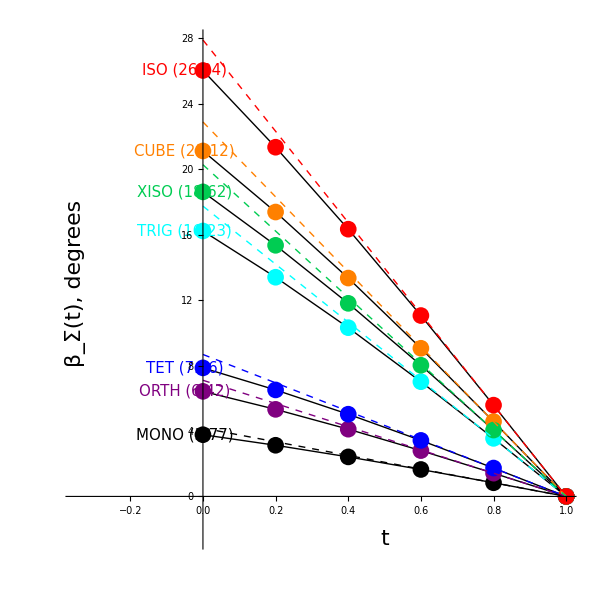

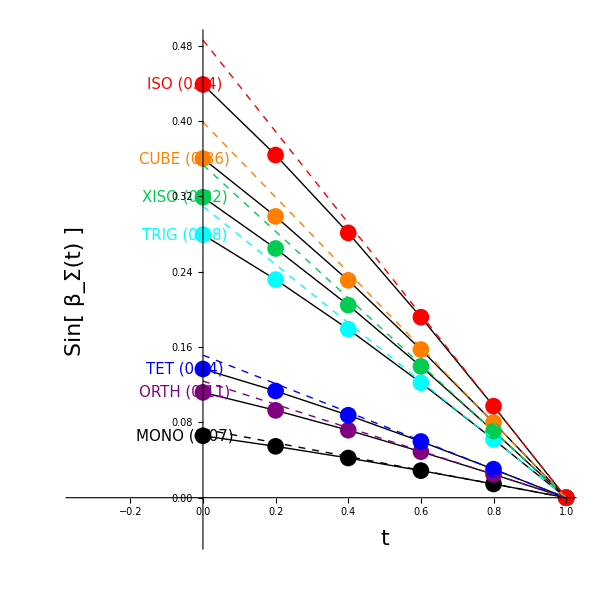

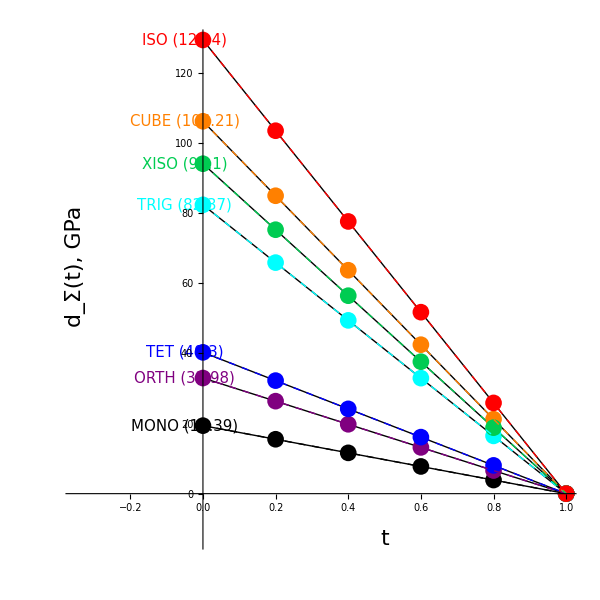

#### Brown: t = –0.6 to t = 1, dt = 0.2, ListSigma = all

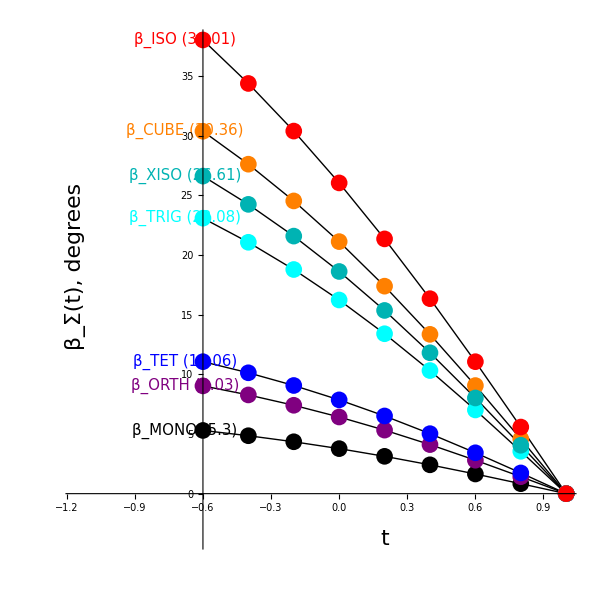

#### Brown: dt = 0.05, Tmat1=TTET, Tmat2=TXISO, ListSigma = {MONO,TET,XISO} [supp1]

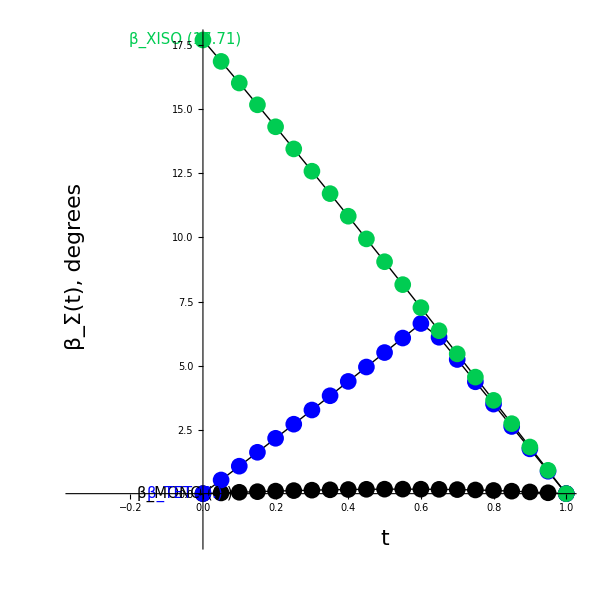

#### The maps from t=0 to t=1 are slightly trivial, as evidence from the small betaMONO angles:

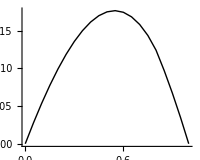

#### Brown: dt = 0.05, Tmat1=TTET, Tmat2=TCUBE, ListSigma={MONO,TET} [supp2]

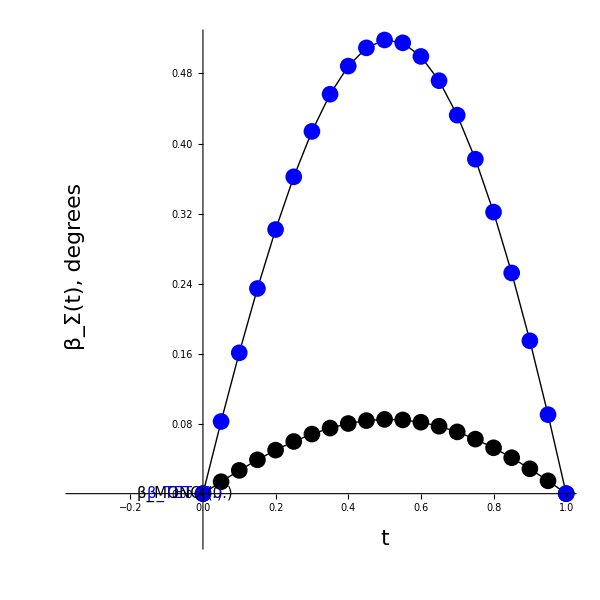

#### Brown: dt = 0.05, Tmat1=TTRIG, Tmat2=TCUBE, ListSigma={MONO,TET,TRIG} [supp3]

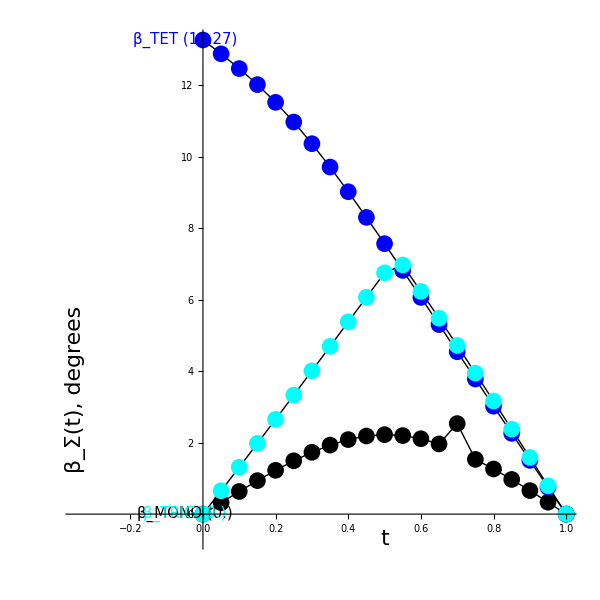

#### Brown dt = 0.05, Tmat1=TORTH, Tmat2=TTET, ListSigma = {TET}, nm1 with UforNM1 = UXISO [supp4]

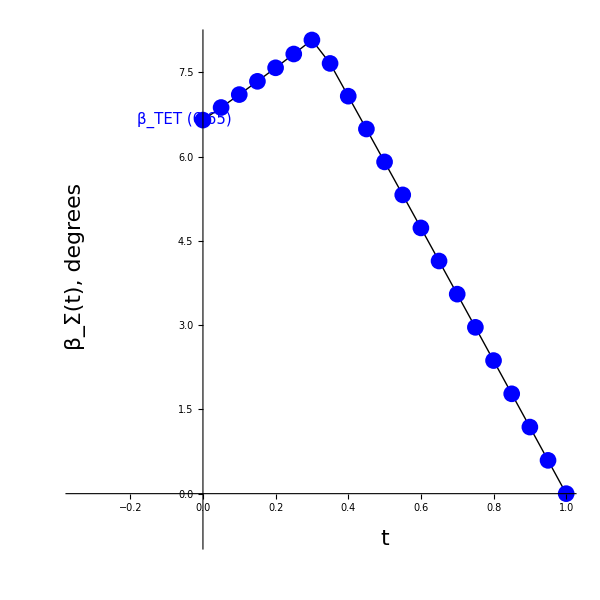

#### Igel dt = 0.05, Tmat1=TTET, Tmat2=TCUBE, ListSigma = {XISO}, nm1 with UforNM1 = UXISO [supp5]

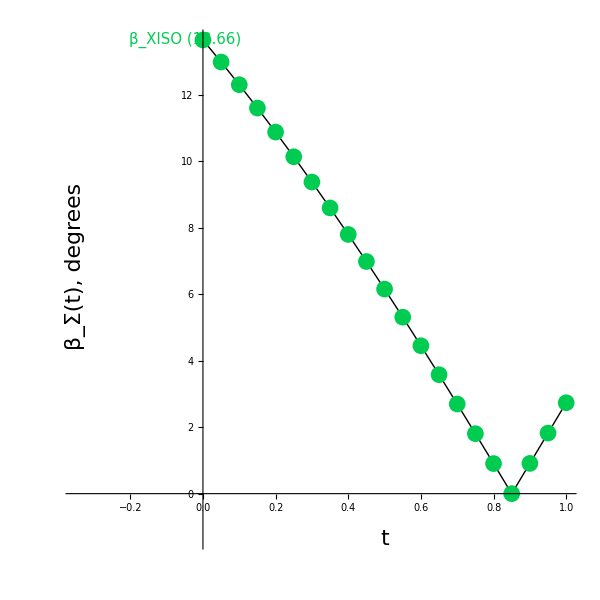

#### SSA2023 dt = 0.05, Tmat1=TMONO, Tmat2=TTRIG, ListSigma = {MONO,ORTH,TET}, nm2 [example 6]